```mathematica
pnf1[y_]=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
pnf2[y_]=Simplify[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
pnf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
qnf1[y_]=Simplify[qf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
qnf2[y_]=Simplify[qf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
qnf3=qf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
png1[y_]=Simplify[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
png2[y_]=Simplify[g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
png3=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
qng1[y_]=Simplify[qg12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
qng2[y_]=Simplify[qg22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
qng3=qg32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
pinf1[y_]:=NIntegrate[pnf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ping1[y_]:=NIntegrate[png1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
pinf2[y_]:=NIntegrate[pnf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ping2[y_]:=NIntegrate[png2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
qinf1[y_]:=NIntegrate[qnf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
qing1[y_]:=NIntegrate[qng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
qinf2[y_]:=NIntegrate[qnf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
qing2[y_]:=NIntegrate[qng2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
qlf1=ParallelTable[{y,qinf1[y]},{y,0,0.9,0.01}];
qlg1=ParallelTable[{y,qing1[y]},{y,0,0.9,0.01}];
qlf2=ParallelTable[{y,qinf2[y]},{y,0.9,1.1,0.01}];
qlg2=ParallelTable[{y,qing2[y]},{y,0.9,1.1,0.01}];
plf1=ParallelTable[{y,pinf1[y]},{y,0,0.9,0.01}];
plg1=ParallelTable[{y,ping1[y]},{y,0,0.9,0.01}];
plf2=ParallelTable[{y,pinf2[y]},{y,0.9,1.1,0.01}];
plg2=ParallelTable[{y,ping2[y]},{y,0.9,1.1,0.01}];
```

```mathematica
psf1=Interpolation[plf1];
psf2=Interpolation[plf2];
psg1=Interpolation[plg1];
psg2=Interpolation[plg2];
qsf1=Interpolation[qlf1];
qsf2=Interpolation[qlf2];
qsg1=Interpolation[qlg1];
qsg2=Interpolation[qlg2];
```

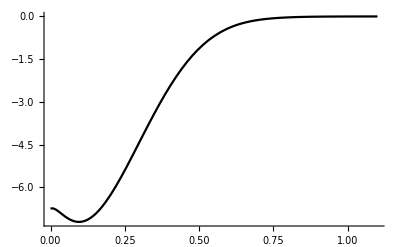
-Graphics-f_syξ=0.1

```mathematica
Labeled[Show[Plot[(-I)*psf1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*psf2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,s],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

```mathematica
pathpf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"p-f-0.1.pdf"}];
Export[pathpf01,Labeled[Show[Plot[(-I)*psf1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*psf2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,p],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\p-f-0.1.pdf

```mathematica
pathpg01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"p-g-0.1.pdf"}];
Export[pathpg01,Labeled[Show[Plot[(-I)*psg1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*psg2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,p],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\p-g-0.1.pdf

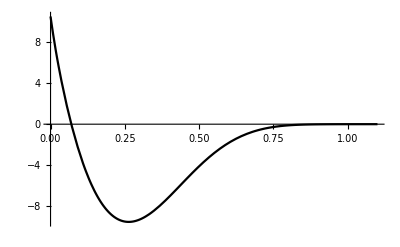
-Graphics-g_pyξ=0.1

```mathematica
Labeled[Show[Plot[(-I)*psg1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*psg2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,p],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

```mathematica
pathqf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"q-f-0.1.pdf"}];
Export[pathqf01,Labeled[Show[Plot[(-I)*qsf1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*qsf2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,q],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\q-f-0.1.pdf

```mathematica
pathqg01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"q-g-0.1.pdf"}];
Export[pathqg01,Labeled[Show[Plot[(-I)*qsg1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*qsg2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,q],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\q-g-0.1.pdf